```mathematica
(* Paul Popa *)
```

```mathematica
(* Midpoint / Shooting HW *)
```

```mathematica
(* Section 6.2 Exercise 1 *)
```

```mathematica
(* Forward Euler *)
```

```mathematica
x0=0;
```

```mathematica
u0=1;
```

```mathematica
deltax=0.1;
```

```mathematica
list1={};
```

```mathematica
For[i=1,i≤10,i++,
u0=u0+2*E^(2*i*deltax);
AppendTo[list1,u0]
];
```

```mathematica
list1
```

{3.44281,6.42645,10.0707,14.5218,19.9583,26.5986,34.709,44.615,56.7143,71.4924}

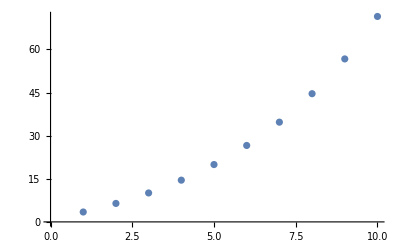

```mathematica
ListPlot[list1]
```

```mathematica
(* Midpoint Method *)
```

```mathematica
list2={};
```

```mathematica
uinit=1;
```

```mathematica
For[i=1,i≤10,i++,
uinit=uinit+2*(uinit+2*E^(2*i*deltax)*(deltax/2))*deltax;
AppendTo[list2,uinit]
];
```

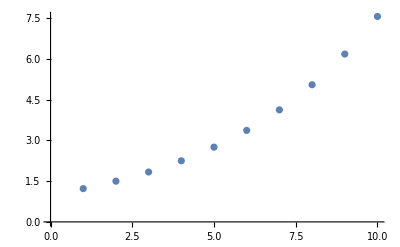

```mathematica
ListPlot[list2]
```

```mathematica
ListPlot[{list1,list2},PlotLabels->{"Forward Euler","Midpoint Method"}]
```

-Graphics-

```mathematica
(* Section 6.3 Exercise 1 *)
```

```mathematica
uinitial=4.5;
```

```mathematica
list3={};
```

```mathematica
For[i=1,i≤10,i++,
v0=2*E^(2*i*deltax)+0.23*((uinitial+2*E^(2*i*deltax)*(deltax/2))^4-3^4)*deltax;
uinitial=uinitial+2*E^(2*i*deltax)*deltax;
AppendTo[list3,v0]
];
```

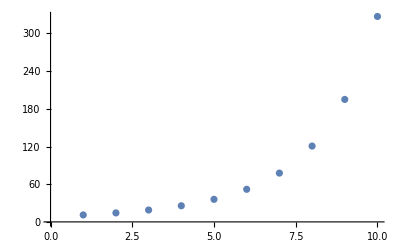

```mathematica
ListPlot[list3]
```